### 非线性Bloch波

```mathematica
-1/2(∂^2 ϕ)/(∂x^2)+v cos(x) ϕ+σ(|ϕ|)^2 ϕ=μ ϕ      (1)
令ϕ(x)=e^ikx ρ(x)         (2)
(2)代入(1)，得到
-1/2(e^ikx(-k^2 ρ(x)+2i k(∂ρ(x))/(∂x)+(∂^2 ρ(x))/(∂x^2)))+v cos(x) e^ikx ρ(x)+σ(|ρ(x)|)^2 e^ikx ρ(x)=μ e^ikx ρ(x)            (3)
约去e^ikx，得到
-1/2(-k^2 ρ(x)+2i k(∂ρ(x))/(∂x)+(∂^2 ρ(x))/(∂x^2))+v cos(x) ρ(x)+σ(|ρ(x)|)^2 ρ(x)=μ ρ(x)    (4)
令 ρ(x)=∑_(m=-L)^L Subscript[a, m] e^imx，代入(4)得到
-1/2(-k^2∑_(m=-L)^L Subscript[a, m] e^imx+2i k(∂ρ(x))/(∂x)+(∂^2 ρ(x))/(∂x^2))+v cos(x) ∑_(m=-L)^L Subscript[a, m] e^imx+σ(|∑_(m=-L)^L Subscript[a, m] e^imx|)^2∑_(m=-L)^L Subscript[a, m] e^imx=μ ∑_(m=-L)^L Subscript[a, m] e^imx
1/2 k^2∑_(m=-L)^L Subscript[a, m] e^imx+k∑_(m=-L)^L m Subscript[a, m] e^imx+1/2∑_(m=-L)^L m^2 Subscript[a, m] e^imx+1/2 v∑_(m=-L)^L Subscript[a, m](e^(i(m+1)x)+e^(i(m-1)x))+σ(|∑_(m=-L)^L Subscript[a, m] e^imx|)^2∑_(m=-L)^L Subscript[a, m] e^imx=μ ∑_(m=-L)^L Subscript[a, m] e^imx
(|∑_(m=-L)^L Subscript[a, m] e^imx|)^2=∑_(m=-L)^L Subscript[a, m] e^-imx∑_(m=-L)^L Subscript[a, m] e^imx=∑_(m=-L)^L Subscript[a, m] e^-imx∑_(n=-L)^L Subscript[a, n] e^inx=∑_(m=-L)^L ∑_(n=-L)^L (Subscript[a, m] Subscript[a, n] e^(i(n-m)x))
(|∑_(m=-L)^L Subscript[a, m] e^imx|)^2∑_(m=-L)^L Subscript[a, m] e^imx=∑_(m=-L)^L ∑_(n=-L)^L (Subscript[a, m] Subscript[a, n] e^(i(n-m)x))∑_(l=-L)^L Subscript[a, l] e^ilx=∑_(m=-L)^L ∑_(n=-L)^L ∑_(l=-L)^L Subscript[a, m] Subscript[a, n] Subscript[a, l] e^(i(n-m+l)x)
e^imx 对应的方程两边系数相等
(1/2 k^2+k m+1/2 m^2)Subscript[a, m]+1/2 v Subscript[a, m+1]+1/2 v Subscript[a, m-1]+∑_(l-g+n=m) Subscript[a, g] Subscript[a, l] Subscript[a, n]=Subscript[μa, m]
(1/2 k^2+k m+1/2 m^2-μ)Subscript[a, m]+1/2 v Subscript[a, m+1]+1/2 v Subscript[a, m-1]+∑_(l-g+n=m) Subscript[a, g] Subscript[a, l] Subscript[a, n]=0
m取值-L到L,
Subscript[f, -L](Subscript[a, -L],Subscript[a, -L+1],...,Subscript[a, L],μ)=0
Subscript[f, -L+1](Subscript[a, -L],Subscript[a, -L+1],...,Subscript[a, L],μ)=0
...
Subscript[f, L](Subscript[a, -L],Subscript[a, -L+1],...,Subscript[a, L],μ)=0
```

{4.99304×10^-9,-8.22017×10^-9,-2.44993×10^-7,9.60762×10^-7,0.0000109324,-0.0000725303,-0.000450209,0.00424305,0.0208007,-0.270555,0.608592,-0.270555,0.0208007,0.00424305,-0.000450209,-0.0000725303,0.0000109324,9.60762×10^-7,-2.44993×10^-7,-8.22017×10^-9,4.99304×10^-9}

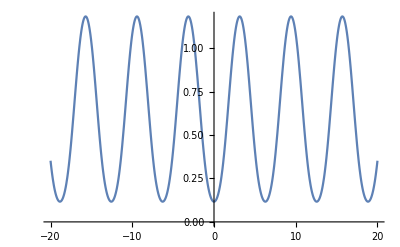

```mathematica
variables={a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16,a17,a18,a19,a20,a21};
Findlgn[m_,L_]:=
Module[{l,g,n,result=0},
For[l=-L,l<=L,l++,
For[g=-L,g<=L,g++,
For[n=-L,n<=L,n++,
If[l-g+n==m,result +=variables[[g+L+1]]*variables[[l+L+1]]*variables[[n+L+1]]]
]]];
result
];
(*Length[Findlgn[5,10]]*)

Geneq[m_,L_,k_,v_,μ_]:=
Module[{},
Switch[m,L,(1/2 k^2+k m+1/2 m^2-μ)variables[[m+L+1]]+1/2 v variables[[m-1+L+1]]+Findlgn[m,L],
-L,(1/2 k^2+k m+1/2 m^2-μ)variables[[m+L+1]]+1/2 v variables[[m+1+L+1]]+Findlgn[m,L],
_,(1/2 k^2+k m+1/2 m^2-μ)variables[[m+L+1]]+1/2 v variables[[m+1+L+1]]+1/2 v variables[[m-1+L+1]]+Findlgn[m,L]
]];
(*Geneq[10,10,0,1.5,-0.3]*)
eqs={};
For[i=-10,i≤10,i++,AppendTo[eqs,Geneq[i,10,0,1.5,0.16]==0]];
init={};
as={5.736132159106507*^-13,-3.894535751922008*^-11,2.1503059846973*^-9,-9.434831682928697*^-8,3.1957675081055905*^-6,-0.00008052891690199129,0.0014378535084812692,-0.01702245838443734,0.12160283282816534,-0.45659687979166724,0.7435592813022905,-0.4565968797916663,0.12160283282816504,-0.017022458384437333,0.0014378535084812673,-0.00008052891690199133,3.1957675081055838*^-6,-9.434831682928685*^-8,2.1503059846972974*^-9,-3.894535751922003*^-11,5.736132159106496*^-13};
For[i=1,i≤21,i++,AppendTo[init,{variables[[i]],as[[i]]}]];

result=variables/.FindRoot[eqs,init]
ϕ1[x_]:=(*-ⅈ**)∑_(m=-10)^10 result[[m+11]] ⅇ^(ⅈ m x);
PicNonLinear=Plot[ϕ1[x],{x,-20,20}]
```

{-0.0000208155,0.0000612686,-0.000180359,0.000529283,-0.00155684,0.00464917,-0.0133849,0.0381213,-0.154672,0.462382,-1.51759×10^-16,-0.462382,0.154672,-0.0381213,0.0133849,-0.00464917,0.00155684,-0.000529283,0.000180359,-0.0000612686,0.0000208155}

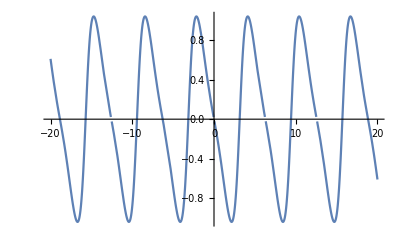

```mathematica
eqs={};
For[i=-10,i≤10,i++,AppendTo[eqs,Geneq[i,10,0,1.5,0.9837580593469167]==0]];
init={};
as={-2.526296353700014*^-12,1.6785075869935976*^-10,-9.023609614724032*^-9,3.82807103472581*^-7,-0.000012409788719563118,0.0002946570630642517,-0.004832175595325367,0.050160197447700124,-0.28483141816551155,0.6452376158593934,1.9102870866168985*^-15,-0.6452376158593918,0.28483141816551116,-0.05016019744770021,0.004832175595325372,-0.00029465706306425253,0.000012409788719563123,-3.828071034725815*^-7,9.023609614724043*^-9,-1.678507586993599*^-10,2.526296353700014*^-12};
For[i=1,i≤21,i++,AppendTo[init,{variables[[i]],as[[i]]}]];

result=variables/.FindRoot[eqs,init]
ϕ2[x_]:=-ⅈ*∑_(m=-10)^10 result[[m+11]] ⅇ^(ⅈ m x);
PicNonLinear2=Plot[ϕ2[x],{x,-20,20}]
```

### 线性Bloch波

```mathematica
∑_(m=-L)^L (k^2+2m k+m^2-2E)Subscript[a, m] e^imx+v ∑_(m=-L)^L Subscript[a, m](e^(i(m+1)x)+e^(i(m-1)x)) =0
方程左边e^imx 的系数应该等于0
...
+(k^2+2L k+L^2-2E)Subscript[a, L] e^iLx+v Subscript[a, L](e^(i(L+1)x)+e^(i(L-1)x))
+(k^2+2(L-1) k+(L-1)^2-2E)Subscript[a, L-1] e^(i(L-1)x)+v Subscript[a, L-1](e^iLx+e^(i(L-2)x))
+(k^2+2(L-2) k+(L-2)^2-2E)Subscript[a, L-2] e^(i(L-2)x)+v Subscript[a, L-2](e^(i(L-1)x)+e^(i(L-3)x))
+...
+(k^2+2(-L+1) k+(-L+1)^2-2E)Subscript[a, -L+1] e^(i(-L+1)x)+v Subscript[a, -L+1](e^(i(-L+2)x)+e^(i(-L)x))
+(k^2+2(-L) k+(-L)^2-2E)Subscript[a, -L] e^(i(-L)x)+v Subscript[a, -L](e^(i(-L+1)x)+e^(i(-L-1)x))
+...=0

(1/2 k^2+L k+1/2 L^2)Subscript[a, L]+1/2 v Subscript[a, L-1]=E Subscript[a, L]
(1/2 k^2+(L-1) k+1/2(L-1)^2)Subscript[a, L-1]+1/2 v Subscript[a, L-2]+1/2 v Subscript[a, L]=E Subscript[a, L-1]
...
(1/2 k^2+(-L+1) k+1/2(-L+1)^2)Subscript[a, -L+1]+1/2 v Subscript[a, -L]+1/2 v Subscript[a, -L+2]=E Subscript[a, -L+1]
(1/2 k^2+(-L) k+1/2(-L)^2)Subscript[a, -L]+1/2 v Subscript[a, -L-1]+1/2 v Subscript[a, -L+1]=E Subscript[a, -L]
```

```mathematica
H1[k_,L_,v_]:=
Module[{M=Table[0,2 L+1,2 L+1]},
For[i=0,i<2L+1,i++,M[[i+1,i+1]]=1/2 k^2+(i-L) k+1/2(i-L)^2];
For[i=0,i<2L,i++,M[[i+1,i+2]]=1/2 v;M[[i+2,i+1]]=1/2 v;];
M
]
Print[H1[-0.5,10,1.5]]
```

{{55.125,0.75,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.75,45.125,0.75,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.75,36.125,0.75,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.75,28.125,0.75,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0.75,21.125,0.75,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.75,15.125,0.75,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0.75,10.125,0.75,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.75,6.125,0.75,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0.75,3.125,0.75,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.75,1.125,0.75,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0.75,0.125,0.75,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.75,0.125,0.75,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0.75,1.125,0.75,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.75,3.125,0.75,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0.75,6.125,0.75,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.75,10.125,0.75,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.75,15.125,0.75,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.75,21.125,0.75,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.75,28.125,0.75,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.75,36.125,0.75},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.75,45.125}}

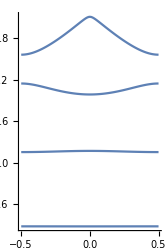

```mathematica
E1=Table[{k,Take[Sort[Eigenvalues[H1[k,10,1.5]]],4]},{k,-0.5,0.5,0.01}];
Points1={};
Points2={};
Points3={};
Points4={};
For[i=1,i<=Length[E1],i++,
AppendTo[Points1,{E1[[i,1]],E1[[i,2,1]]}];AppendTo[Points2,{E1[[i,1]],E1[[i,2,2]]}];AppendTo[Points3,{E1[[i,1]],E1[[i,2,3]]}];AppendTo[Points4,{E1[[i,1]],E1[[i,2,4]]}]
];
P1=ListLinePlot[Points1];
P2=ListLinePlot[Points2];
P3=ListLinePlot[Points3];
P4=ListLinePlot[Points4];
Show[P1,P2,P3,P4,PlotRange->All,AspectRatio->1.5,AxesOrigin->{-0.5,-1.0}]
```

```mathematica
Eigenvalues[H1[0,10,1.5]]
```

{50.059,50.059,40.5071,40.5071,32.0088,32.0088,24.5115,24.5115,18.0157,18.0157,12.5228,12.5228,8.03583,8.03583,4.56538,4.56463,2.2111,2.10558,0.983758,-0.921104,0.168923}

```mathematica
Eigensystem[H1[0,10,1.5]]
```

{{50.059,50.059,40.5071,40.5071,32.0088,32.0088,24.5115,24.5115,18.0157,18.0157,12.5228,12.5228,8.03583,8.03583,4.56538,4.56463,2.2111,2.10558,0.983758,-0.921104,0.168923},{{1.80312×10^-18,1.41936×10^-19,5.90184×10^-21,1.73302×10^-22,4.05769×10^-24,1.45626×10^-25,3.23507×10^-24,1.81273×10^-22,1.10083×10^-20,7.05215×10^-19,4.65887×10^-17,3.10887×10^-15,2.05384×10^-13,1.31576×10^-11,7.9906×10^-10,4.47971×10^-8,2.24258×10^-6,0.0000958152,0.00326302,0.0784734,0.996911},{0.996911,0.0784734,0.00326302,0.0000958152,2.24258×10^-6,4.47971×10^-8,7.9906×10^-10,1.31576×10^-11,2.05384×10^-13,3.10887×10^-15,4.65887×10^-17,7.05215×10^-19,1.10083×10^-20,1.81273×10^-22,3.23218×10^-24,-1.64237×10^-26,-4.05466×10^-24,-1.73302×10^-22,-5.90184×10^-21,-1.41936×10^-19,-1.80312×10^-18},{-4.1282×10^-15,5.22513×10^-14,4.62567×10^-15,2.17071×10^-16,7.23987×10^-18,1.94052×10^-19,6.58778×10^-21,9.14813×10^-20,4.38539×10^-18,2.25067×10^-16,1.20013×10^-14,6.47961×10^-13,3.45521×10^-11,1.77335×10^-9,8.51033×10^-8,3.68685×10^-6,0.000137592,0.00412539,0.08791,0.993025,-0.0784557},{-0.0784557,0.993025,0.08791,0.00412539,0.000137592,3.68685×10^-6,8.51033×10^-8,1.77335×10^-9,3.45521×10^-11,6.47961×10^-13,1.20013×10^-14,2.25067×10^-16,4.38538×10^-18,9.12947×10^-20,-2.36819×10^-21,-1.93939×10^-19,-7.23987×10^-18,-2.17071×10^-16,-4.62567×10^-15,-5.22513×10^-14,4.1282×10^-15},{6.99313×10^-11,-1.67753×10^-9,1.89223×10^-8,1.90019×10^-9,1.01942×10^-10,3.92378×10^-12,1.22679×10^-13,3.38675×10^-15,1.54177×10^-15,5.83021×10^-14,2.44783×10^-12,1.04411×10^-10,4.38406×10^-9,1.7531×10^-7,6.4257×10^-6,0.000205523,0.00533958,0.0995295,0.991126,-0.0878667,0.00366291},{0.00366291,-0.0878667,0.991126,0.0995295,0.00533958,0.000205523,6.4257×10^-6,1.7531×10^-7,4.38406×10^-9,1.04411×10^-10,2.44783×10^-12,5.82981×10^-14,1.37437×10^-15,-3.30718×10^-15,-1.22676×10^-13,-3.92378×10^-12,-1.01942×10^-10,-1.90019×10^-9,-1.89223×10^-8,1.67753×10^-9,-6.99313×10^-11},{-3.62651×10^-8,1.23245×10^-6,-0.0000262371,0.000260735,0.0000302496,1.89417×10^-6,8.61853×10^-8,3.23414×10^-9,1.0827×10^-10,1.56141×10^-11,3.91621×10^-10,1.27834×10^-8,4.08873×10^-7,0.0000122597,0.000326705,0.00718027,0.114668,0.988375,-0.0994578,0.0046719,-0.000137471},{-0.000137471,0.0046719,-0.0994578,0.988375,0.114668,0.00718027,0.000326705,0.0000122597,4.08873×10^-7,1.27834×10^-8,3.91414×10^-10,8.86953×10^-12,-1.07453×10^-10,-3.23411×10^-9,-8.61852×10^-8,-1.89417×10^-6,-0.0000302496,-0.000260735,0.0000262371,-1.23245×10^-6,3.62651×10^-8},{2.93386×10^-6,-0.000125116,0.00374793,-0.0697576,0.599354,0.0823386,0.00619149,0.000344468,0.0000161636,6.94953×10^-7,6.6572×10^-8,9.04172×10^-7,0.0000210498,0.000448599,0.00806315,0.107229,0.780536,-0.0908451,0.00488092,-0.000162939,3.82075×10^-6},{3.82075×10^-6,-0.000162939,0.00488092,-0.0908451,0.780536,0.107229,0.00806315,0.000448599,0.0000210496,9.01691×10^-7,8.74106×10^-9,-6.91722×10^-7,-0.0000161634,-0.000344468,-0.00619149,-0.0823386,-0.599354,0.0697576,-0.00374793,0.000125116,-2.93386×10^-6},{-1.23914×10^-7,6.19193×10^-6,-0.000230854,0.005989,-0.0954114,0.6908,0.11637,0.0109521,0.000784111,0.0000492824,5.90311×10^-6,0.0000492818,0.000784102,0.0109519,0.116369,0.690791,-0.0954102,0.00598892,-0.000230851,6.19185×10^-6,-1.23912×10^-7},{1.23912×10^-7,-6.19185×10^-6,0.000230851,-0.00598892,0.0954102,-0.690791,-0.116369,-0.0109519,-0.000784075,-0.0000489119,3.55908×10^-11,0.0000489125,0.000784085,0.0109521,0.11637,0.6908,-0.0954114,0.005989,-0.000230854,6.19193×10^-6,-1.23914×10^-7},{5.16719×10^-9,-2.89116×10^-7,0.0000125094,-0.000399414,0.00875551,-0.115923,0.681242,0.148464,0.0186833,0.00189465,0.000353663,0.00189465,0.0186833,0.148464,0.681242,-0.115923,0.00875551,-0.000399414,0.0000125094,-2.89116×10^-7,5.16719×10^-9},{-5.1672×10^-9,2.89116×10^-7,-0.0000125094,0.000399414,-0.00875551,0.115923,-0.681243,-0.148463,-0.0186788,-0.001859,-2.01637×10^-12,0.001859,0.0186788,0.148463,0.681243,-0.115923,0.00875551,-0.000399414,0.0000125094,-2.89116×10^-7,5.1672×10^-9},{-2.77486×10^-10,1.681×10^-8,-8.05135×10^-7,0.0000294346,-0.000781553,0.0139704,-0.147018,0.659298,0.20449,0.0401594,0.0131948,0.0401594,0.20449,0.659298,-0.147018,0.0139704,-0.000781553,0.0000294346,-8.05135×10^-7,1.681×10^-8,-2.77486×10^-10},{2.77514×10^-10,-1.68119×10^-8,8.05247×10^-7,-0.0000294395,0.000781711,-0.013974,0.14707,-0.659678,-0.20392,-0.0376269,1.24894×10^-13,0.0376269,0.20392,0.659678,-0.14707,0.013974,-0.000781711,0.0000294395,-8.05247×10^-7,1.68119×10^-8,-2.77514×10^-10},{2.27402×10^-11,-1.44897×10^-9,7.39499×10^-8,-2.93573×10^-6,0.0000871718,-0.00183219,0.0250478,-0.1915,0.559386,0.348947,0.236725,0.348947,0.559386,-0.1915,0.0250478,-0.00183219,0.0000871718,-2.93573×10^-6,7.39499×10^-8,-1.44897×10^-9,2.27402×10^-11},{-2.26666×10^-11,1.44747×10^-9,-7.40771×10^-8,2.95121×10^-6,-0.0000880467,0.00186299,-0.0257315,0.200367,-0.613953,-0.286791,6.53786×10^-15,0.286791,0.613953,-0.200367,0.0257315,-0.00186299,0.0000880467,-2.95121×10^-6,7.40771×10^-8,-1.44747×10^-9,2.26666×10^-11},{-5.4816×10^-12,3.5825×10^-10,-1.88701×10^-8,7.80015×10^-7,-0.0000244385,0.000553689,-0.00847744,0.0787527,-0.360741,0.410047,0.625225,0.410047,-0.360741,0.0787527,-0.00847744,0.000553689,-0.0000244385,7.80015×10^-7,-1.88701×10^-8,3.5825×10^-10,-5.4816×10^-12},{5.73613×10^-13,-3.89454×10^-11,2.15031×10^-9,-9.43483×10^-8,3.19577×10^-6,-0.0000805289,0.00143785,-0.0170225,0.121603,-0.456597,0.743559,-0.456597,0.121603,-0.0170225,0.00143785,-0.0000805289,3.19577×10^-6,-9.43483×10^-8,2.15031×10^-9,-3.89454×10^-11,5.73613×10^-13},{-2.5263×10^-12,1.67851×10^-10,-9.02361×10^-9,3.82807×10^-7,-0.0000124098,0.000294657,-0.00483218,0.0501602,-0.284831,0.645238,1.91029×10^-15,-0.645238,0.284831,-0.0501602,0.00483218,-0.000294657,0.0000124098,-3.82807×10^-7,9.02361×10^-9,-1.67851×10^-10,2.5263×10^-12}}}

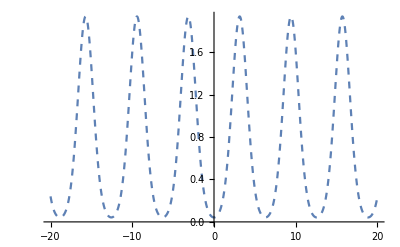

```mathematica
ams={5.736132159106507*^-13,-3.894535751922008*^-11,2.1503059846973*^-9,-9.434831682928697*^-8,3.1957675081055905*^-6,-0.00008052891690199129,0.0014378535084812692,-0.01702245838443734,0.12160283282816534,-0.45659687979166724,0.7435592813022905,-0.4565968797916663,0.12160283282816504,-0.017022458384437333,0.0014378535084812673,-0.00008052891690199133,3.1957675081055838*^-6,-9.434831682928685*^-8,2.1503059846972974*^-9,-3.894535751922003*^-11,5.736132159106496*^-13}; (* 取自倒数第二个特征向量 *)
ϕ[x_]:=∑_(m=-10)^10 ams[[m+11]] ⅇ^(ⅈ m x);
PicLinear=Plot[ϕ[x],{x,-20,20},PlotStyle->Dashed]
```

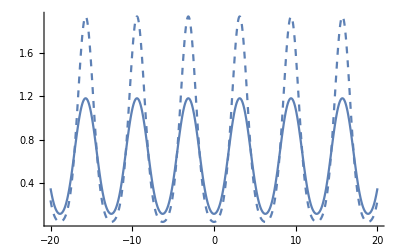

```mathematica
Show[PicNonLinear,PicLinear,PlotRange->All]
```

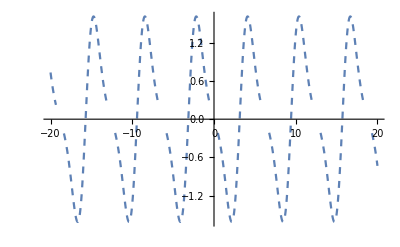

```mathematica
ams2={-2.526296353700014*^-12,1.6785075869935976*^-10,-9.023609614724032*^-9,3.82807103472581*^-7,-0.000012409788719563118,0.0002946570630642517,-0.004832175595325367,0.050160197447700124,-0.28483141816551155,0.6452376158593934,1.9102870866168985*^-15,-0.6452376158593918,0.28483141816551116,-0.05016019744770021,0.004832175595325372,-0.00029465706306425253,0.000012409788719563123,-3.828071034725815*^-7,9.023609614724043*^-9,-1.678507586993599*^-10,2.526296353700014*^-12};(* 取自倒数第一个特征向量 *)
ϕ2[x_]:=-ⅈ*∑_(m=-10)^10 ams2[[m+11]] ⅇ^(ⅈ m x);
PicLinear2=Plot[ϕ2[x],{x,-20,20},PlotStyle->Dashed]
```

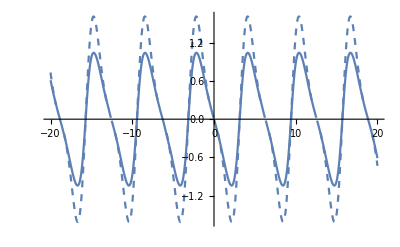

```mathematica
Show[PicNonLinear2,PicLinear2,PlotRange->All]
```